# Linear Regression Model Initialization

## Defining a Function to create Linear Regression Neural Network

#### Explanation

When we create a neural network with each layer having a fully linear activation function (LinearLayer), each layer simply outputs a linear combination of the outputs of the previous layer. Mathematically, this shows itself as 

Layer Output 

where  is a matrix of weights and  is the value of the bias. It’s important to note that you could apply this operation infinite times and the output would still be a linear combination of the original weights and biases. This portion of the project will examine how changes in the distributions of weights and biases affect the outputs of a linear regression neural network and how the behavior changes with increases depths.

```mathematica
LinearRegressionNetworkPlot[depths_,distributionType_,params_]:=Module[{netInit,f,plots,depth,distribution,title},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
title="Outputs of Linear Regression Network with Weights initialized from a "<>distributionType <> " distribution.";
plots=Table[With[{netInit=NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}]},Column[{Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[{x,x,x}];
SetAttributes[f,Listable];
f[x]],15],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None],Style["depth = "<>ToString[depth],Italic,12,Gray]}]],{depth,depths}];
Column[{Style[title,Bold,14],Row[Riffle[plots,Spacer[20]]]}]]
```

#### Explanation

This function generates plots of outputs for 15 runs of neural networks with inputted depth that have weights generated from an inputted distribution (either Normal, Gamma, or Uniform), and based on the distribution type, takes either one or two parameters for generating the distribution. It then plots the outputs of each run of the neural network for each of the inputted depths, showing a clear progression of the complexity of outputs as depth increases.

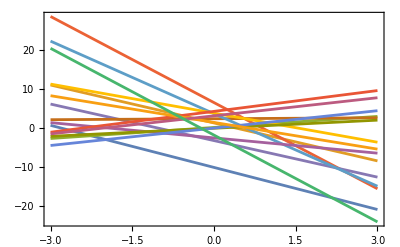
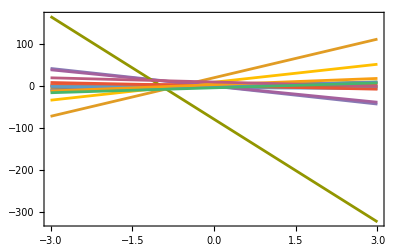
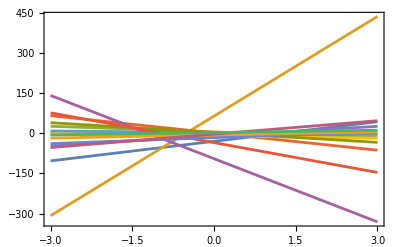
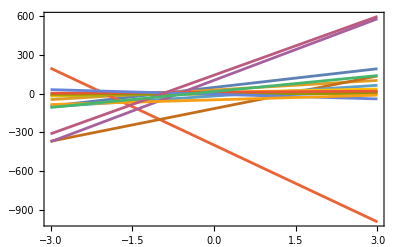
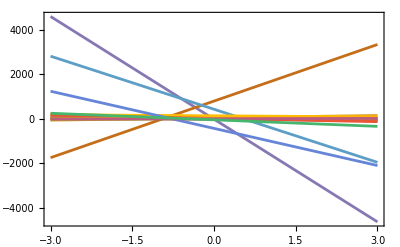
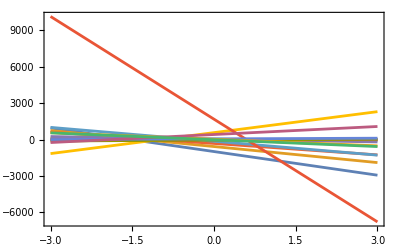
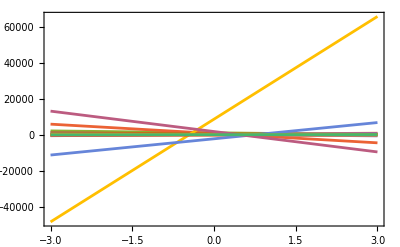
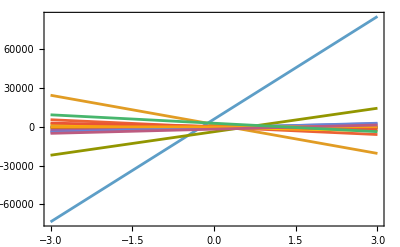
Outputs of Linear Regression Network with Weights initialized from a Normaldistribution.
-Graphics-
depth = 1-Graphics-
depth = 2-Graphics-
depth = 3-Graphics-
depth = 4-Graphics-
depth = 5-Graphics-
depth = 6-Graphics-
depth = 7-Graphics-
depth = 8

```mathematica
LinearRegressionNetworkPlot[Range[8],"Normal",{0,1}]
```

#### Explanation

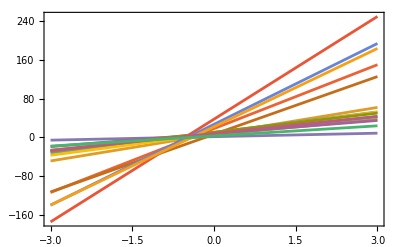
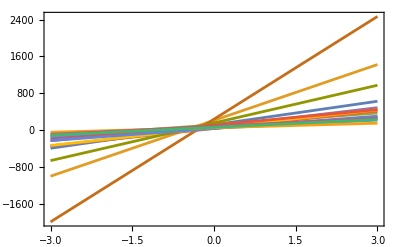
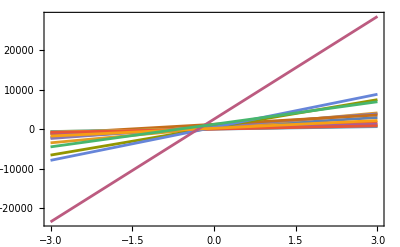
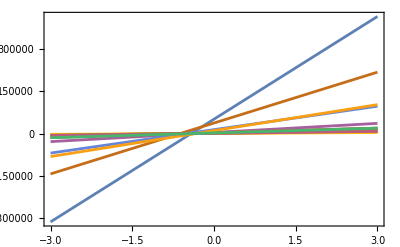
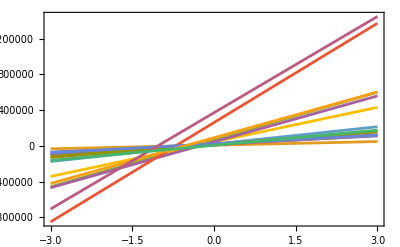
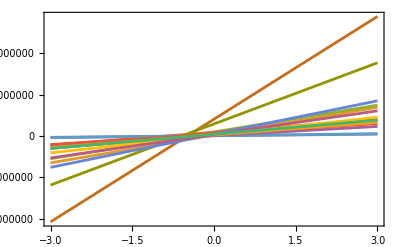
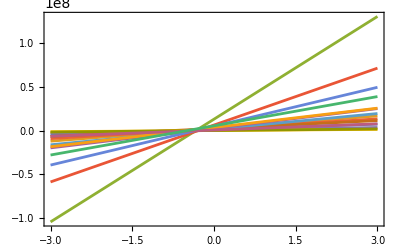
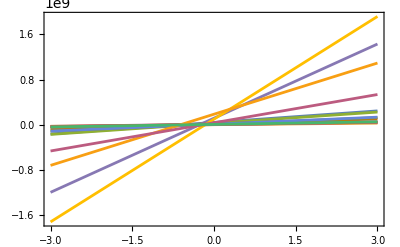
Outputs of Linear Regression Network with Weights initialized from a Gamma distribution.
-Graphics-
depth = 1-Graphics-
depth = 2-Graphics-
depth = 3-Graphics-
depth = 4-Graphics-
depth = 5-Graphics-
depth = 6-Graphics-
depth = 7-Graphics-
depth = 8

```mathematica
LinearRegressionNetworkPlot[Range[8],"Gamma",{1,1}]
```

#### Explanation

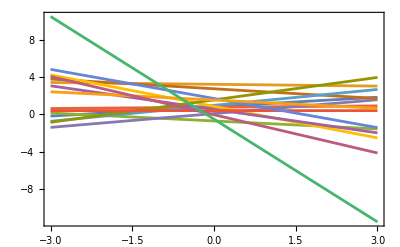
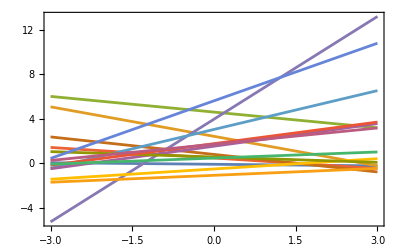
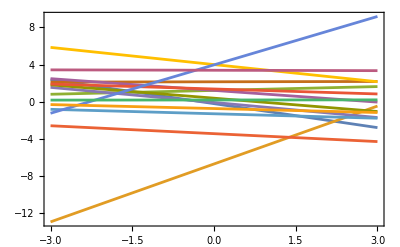
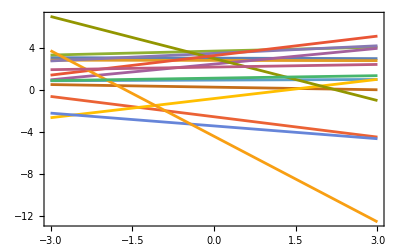
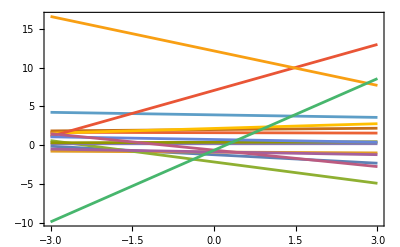
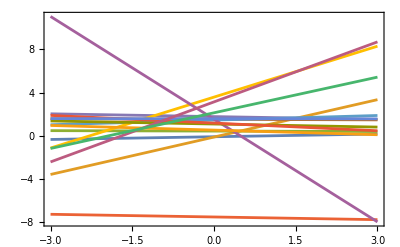
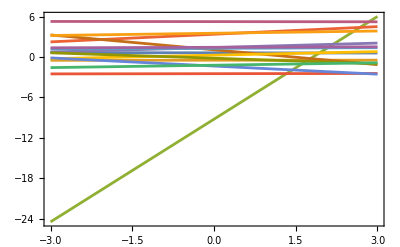
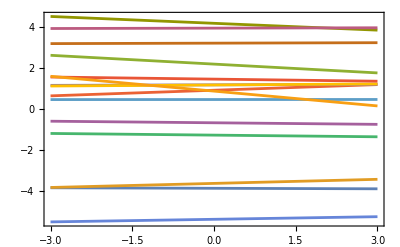
Outputs of Linear Regression Network with Weights initialized from a Uniform distribution.
-Graphics-
depth = 1-Graphics-
depth = 2-Graphics-
depth = 3-Graphics-
depth = 4-Graphics-
depth = 5-Graphics-
depth = 6-Graphics-
depth = 7-Graphics-
depth = 8

```mathematica
LinearRegressionNetworkPlot[Range[8],"Uniform",{1}]
```

#### Explanation

```mathematica
Manipulate[Module[{netInit,f,plots,distribution,title},distribution=NormalDistribution[0,stdDev];
SeedRandom[1234];
title="Outputs of Linear Regression Network with Weights initialized from Normal Distribution";
plots=Table[With[{netInit=NetChain[Append[Catenate@Table[{3,LinearLayer[3]},d],LinearLayer[1]],"Input"->{3}]},Column[{Plot[Evaluate@Flatten@Table[Module[{net=NetInitialize[netInit,Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic],f},f[x_?NumericQ]:=net[{x,x,x}];
SetAttributes[f,Listable];
f[x]],1],{x,-3,3},PlotRange->Full,Frame->True,FrameTicks->None],Style["depth = "<>ToString[d],Italic,12,Gray]}]],{d,depth}];
Column[{Style[title,Bold,14],Row[Riffle[plots,Spacer[20]]]}]],{{depth,1,"Depth"},1,10,1},{{stdDev,1,"Standard Deviation"},0.1,5,0.1}]
```

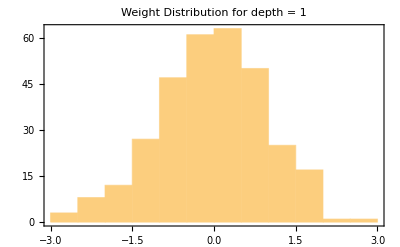
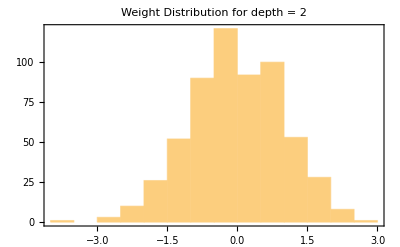
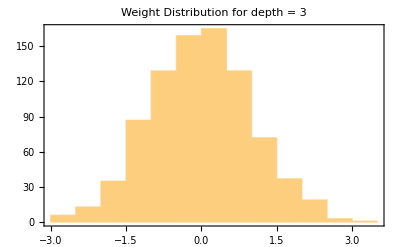
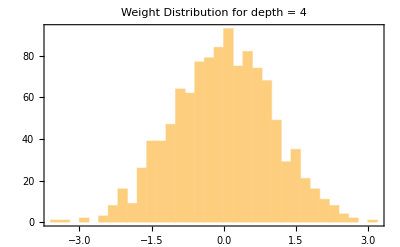
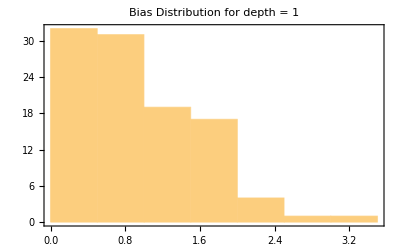
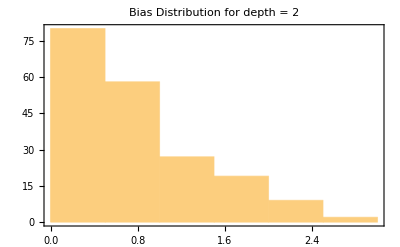
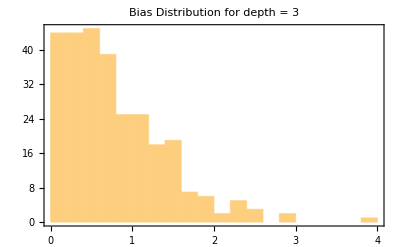
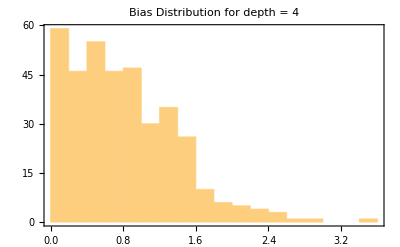
Weight and Bias Distributions
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
WeightBiasDistributionHistograms[depths_,distributionType_,params_]:=Module[{netInit,distribution,weightPlots,biasPlots,weights,biases},distribution=Switch[distributionType,"Normal",NormalDistribution[params[[1]],params[[2]]],"Uniform",UniformDistribution[{-params[[1]],params[[1]]}],"Gamma",GammaDistribution[params[[1]],params[[2]]],_,NormalDistribution[0,1]];
SeedRandom[1234];
weights=Table[Flatten[Table[Module[{net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic]},Normal[NetExtract[net,{All,"Weights"}]]],15]],{depth,depths}];
biases=Table[Flatten[Table[Module[{net=NetInitialize[NetChain[Append[Catenate@Table[{3,LinearLayer[3]},depth],LinearLayer[1]],"Input"->{3}],Method->{"Random","Weights"->distribution,"Biases"->TruncatedDistribution[{0,∞},NormalDistribution[]]},RandomSeeding->Automatic]},Normal[NetExtract[net,{All,"Biases"}]]],15]],{depth,depths}];
weightPlots=Table[Histogram[weights[[i]],PlotLabel->"Weight Distribution for depth = "<>ToString[depths[[i]]],Frame->True],{i,Length[depths]}];
biasPlots=Table[Histogram[biases[[i]],PlotLabel->"Bias Distribution for depth = "<>ToString[depths[[i]]],Frame->True],{i,Length[depths]}];
Column[{Style["Weight and Bias Distributions",Bold,14],Row[Riffle[weightPlots,Spacer[20]]],Row[Riffle[biasPlots,Spacer[20]]]}]]

WeightBiasDistributionHistograms[{1,2,3,4},"Normal",{0,1}]
```